# Notes on "A Method for Normalizing Histology Slides for Quantitative Analysis"

This is a walkthrough of the "unmixing" path of the methods presented in "A Method for Normalizing Histology Slides for Quantitative Analysis", by Marc Macenko, Marc Niethammer, J.S. Marron, David Borland, John T. Woosley, Xiaojun Guan, Charles Schmitt, and Nancy E. Thomas, published in the Proceedings of the IEEE International Symposium on Biomedical Imaging: From Nano to Macro, pp. 1107-1110, July 2009.

The authors were approached for access to images, Figures (which were too small to read), and code that might be available. But the response was from the Office of Technology Development, The University of North Carolina at Chapel Hill requesting a commercialization license.

This method is attractive since if has the potential to be thousands of times faster than methods based on PCA, ICA, and NMF, such as the method of Newberg, et al. That estimate is based on the fact that obtaining convergence in the NMF method of Newberg requires thousands of iterations that have at their heart a full singular value decomposition. The method described here requires a single SVD, and "thin" SVD at that.

## Outline of the Method

The key feature of the method appears to be the conversion of RGB data from its native "transmittance" units to absorbance (optical density). The data in absorbance space appear to be linearly separable. The following is largely transcribed from Algorithm 1 in the paper.

Input is an RGB image of a slide.

Convert RGB to OD.

Remove data with an OD less than an empirically-determined constant β.

Calculate a SVD (Singular Value Decomposition) on the OD tuples.

Create a plane from the SVD directions corresponding to the two largest singular values.

Project data on the plane, and normalize it to unit length.

Calculate the angle of each point with respect to the first SVD direction.

Find robust extremes (α^th and (100 - α^th) percentiles of the angle.

Convert extreme values back to OD space.

Output is the optimal stain vectors.

### An RGB Image

Open and retrieve an RGB image for use later in the computations. (Note: You will likely need to change the following path to the image file to match the directory layout on your machine.)

```mathematica
imgPath = "C:\\projects\\color-deconvolution\\Images\\3356_001_11889L_9990T.jpg";
img = Import[imgPath]
```

-Graphics-

```mathematica
Dimensions[ImageData[img]]
```

{100,100,3}

#### About this Image

This is a small portion of SI Serialized Slide Number 2861, ScanScope slide number 3356. It is a 100x100 pixel sub-image located at 11,889 pixels from the left and 9,990 pixels from the top of the original, complete image. It is interesting because it has white space to be thresholded and red cells to trick the algorithm. The red cells do not saturate the red channel as they do in some images. An image from a nearby region without red cells is available in 3356_003_11859L_10084T.jpg.

### Options to Control Computation

These are just some global settings that can be used to control how computations are carried out. They are defined here to assure that they are in scope when functions are defined and evaluated later in the document.

```mathematica
options[verbose] = True;
options[alpha]=0.01;
options[beta] = 0.15;
```

The verbose flag controls the level and detail of debugging/tracing messages. The alpha variable is the same one used in the paper to find robust extremes  of the angle of the pixels with respect to the first SVD directions. The beta variable is taken directly from the paper as well, being the threshold used to eliminate glass background or pixels with very light staining.

### Options to Control Color of Plotted Points

It is easy and instructive to color the individual points in the plots later in these notes. However, it can be very time consuming. (It is by far the slowest step in re-evaluating the notebook -- much slower than the deconvolution itself.) The option here controls the color function used in the remainder of the notebook. To change the behavior, you must come back up here and re-evaluate the following cells before evaluating the plots.

```mathematica
options[colorPts]=True;
ptCf=If[options[colorPts]==True,Function[{r,g,b},RGBColor[r,g,b]],Function[{r,g,b},RGBColor[0,0,0]]];
```

Planes are always displayed using the following color function.

```mathematica
plnCf=Function[{x,y,z},RGBColor[0.8,0.85,0.95]];
```

### Convert RGB to OD

The transformation from RGB to OD is conceptually simple. First, the definition of transmittance.

T=I_out/I_inp

where I_out/I_inp is the fraction of the input intenstiy that makes it through the sample. It is often experssed as a percentage ranging from 0 to 100%. In the case of a scanned image, I_inp is usually related to the resolution of the A/D converter. For an 8-bit camera, the maximum value is 255. However, many scanners, such as the Aperio, calibrate themselves with a smaller value to detect oversaturation. Aperio uses a value of 240, but for simplicity, the description in this explanation will use a value of 255.

The transformation from transmittance to absorbance is almost as straightforward.

OD=-Log10[T]

and ranges in value from 0 (perfectly transparent) to infinity (perfectly opaque.) For numerical analysis reasons, values of 0 are usually replaced with a small number, perhaps the machine precision. Likewise at the other end of the scale, instrumentation is typically unreliable at absorbance values of 3 or greater, so the value of 3 can be used instead of infinity.

Taking a logarithm of every pixel value in an image might be very time consuming, particularly on images of an interesting size. With only 255 possible values, a lookup table might be a faster approach in production code. However, even taking the logarithm is likely to be insignificant compared to the Singular Value Decomposition (see below.)

```mathematica
(* Convert the data in an image to a matrix of RGB tuples. This function removes the row/column structure from the image data.
Input: img -- an image file. Assumed to be an RGB image.
Output: an array of RGB tuples with byte data elements.*)
convertToRgbTuples[img_]:= Flatten[ImageData[img, "Byte"], 1];
```

```mathematica
Short[convertToRgbTuples[img], 3]
```

{{217,133,169},{209,119,157},{216,119,162},{228,126,173},{224,129,173},«9990»,{128,111,153},{165,127,166},{174,136,175},{184,146,183},{184,150,185}}

```mathematica
ListPointPlot3D[convertToRgbTuples[img], ColorFunction->ptCf,AxesLabel -> {"R","G","B"}]
```

-Graphics3D-

The "cloud" of pixels off of the main group at high values of R and low values of G is probably due to red cells.

```mathematica
(* Convert a short integer (8-bit byte) in the range of 0 to 255 to absorbance. Assumes that a value of 0 represents 0% transmittance and that 255 represents 100% transmittance. Handles special cases of 0% and 100% transmittance for numerical stability. Forces the result to a numerical value (as opposed to symbolic) using default machine precision. *)
convertRgbToOD[trans_]:=Module[
{recip},
recip=trans/255;
Switch[recip, 255, 0.000000001, 0, 3.0, _, N[-Log10[recip]]]
];
```

Create a table of absorbance values for all possible input values (0..255). Use the table to lookup absorbance values rather than calculating the value, which would require calls to the logarithm function.

```mathematica
odTable=Table[convertRgbToOD[trans], {trans, 0, 255}];
```

```mathematica
(* Convert an RGB tuple (a list with 3 elements in the range of 0 to 255) to an absorbance tuple.*)
convertRgbTupleToOD[tuple_]:=odTable[[#+1]]&/@tuple;
```

```mathematica
convertRgbTupleToOD[{0, 255, 10}]
```

{3.,0.,1.40654}

```mathematica
(* Convert a list of RGB tuples to absorbance. The input is a list of 3-element lists where each element is a value between 0 and 255.*)convertRgbTupleArrayToOD[tuples_]:=convertRgbTupleToOD /@ tuples;
```

```mathematica
Take[convertRgbTupleArrayToOD[convertToRgbTuples[img]], 3]
```

{{0.0700804,0.282689,0.178653},{0.0863939,0.330993,0.210641},{0.0720864,0.330993,0.197025}}

A plot of the converted pixels does not clearly show the digitization effect due to the transform as is the case with other images that saturate one or more of the channels. This is probably a case where deriving the RGB data from spectral data would provide better results. (It would be an interesting study in itself to compare performance with RGB data derived from spectral data to the results using spectral data itself. It seems like using spectral data would make it easier to deal with more than three dyes as well.)

```mathematica
ListPointPlot3D[convertRgbTupleArrayToOD[convertToRgbTuples[img]],ColorFunction->ptCf,AxesLabel->{"R Abs","G Abs","B Abs"}]
```

-Graphics3D-

### Threshold OD Intensities Less than β

Here is where things start to get a little fuzzy. From the description in the paper, it is not clear if they intend to threshold pixels where any value in the tuple is less than the cutoff or pixels where all of the values are less than the cutoff. My belief is that only pixels where all of the OD values are less than the cutoff should be removed. The intent is to remove pixels with very little stain, indicating no color of any kind, i.e. little color in any of the channels. Further, it is possible to imagine pixels with very little signal in one of the RGB channels but strong signals in the other two. For example, an H&E stain might produce strong red and blue responses, but very little green. Clearly those pixels should be retained.

The paper proposes using a value of 0.15 for β, which seems reasonable in the absence of any other data.

```mathematica
tupleAboveThresholdQ[tuple_]:=Module[
{b},
b=options[beta];
Or[tuple[[1]]>b,tuple[[2]]>b, tuple[[3]]>b]
]
```

```mathematica
thresholdByBeta[odPixels_]:=Select[odPixels, tupleAboveThresholdQ];
```

```mathematica
bdat={{0, 0, 0}, {0, .5, 0}, {1, 1, .5}, {.2, .2, .3},{.1, .1, .05}}
```

{{0,0,0},{0,0.5,0},{1,1,0.5},{0.2,0.2,0.3},{0.1,0.1,0.05}}

```mathematica
thresholdByBeta[bdat]
```

{{0,0.5,0},{1,1,0.5},{0.2,0.2,0.3}}

Since our example image has lots of white background, we can compare the number of pixels in the image (RGB tuples) to the number after thresholding as a "sanity check".

```mathematica
Dimensions[convertToRgbTuples[img]]
```

{10000,3}

```mathematica
Dimensions[thresholdByBeta[convertRgbTupleArrayToOD[convertToRgbTuples[img]]]]
```

{8564,3}

```mathematica
odPts=thresholdByBeta[convertRgbTupleArrayToOD[convertToRgbTuples[img]]];
```

```mathematica
ListPointPlot3D[odPts,ColorFunction->ptCf,AxesLabel->{"R Abs","G Abs","B Abs"}]
```

-Graphics3D-

So, about one eighth of the pixels are eliminated. Seems about right by calibrated eyeball. But it isn't obvious to me where they were from the images.

### Calculate the Singular Value Decomposition on the OD Tuples

Easy enough.

A "thin" SVD associated with the two largest singular values can be calculated as:

```mathematica
{u,s,v}= SingularValueDecomposition[thresholdByBeta[convertRgbTupleArrayToOD[convertToRgbTuples[img]]],2];
```

```mathematica
s//MatrixForm
```

(35.4324 | 0.
0. | 4.76208)

As a note to myself the singular values can be calculated as follows:

```mathematica
calcSingularValues[a_]:= N[Sqrt[Sort[Eigenvalues[Transpose[a].a],Greater]]]
```

```mathematica
sv2=calcSingularValues[thresholdByBeta[convertRgbTupleArrayToOD[convertToRgbTuples[img]]]]
```

{35.4324,4.76208,1.30443}

### Create a Plane from the Directions of the Two Largest Singular Values

Huh? To quote from the paper:

The shortest path between two unit-norm color vectors on the sphere is the geodesic path. This line appears to be curved in a spherical coordinate decomposition unless it would correspond to change in only one direction or the other. By finding this specific geodesic direction, we can project the OD transformed pixels onto it in order to find the endpoints that correspond to the stain vectors.

The first step in this process is to calculate the plane that the vectors form. This is done by forming a plane from the two vectors corresponding to the two largest singular values of the SVD decomposition of the OD transformed pixels. All of these OD transformed pixels are then projected onto this plane, and subsequently normalized to unit length. The projection line is shown to be curved in Figure 3(a). The angle with respect to the first SVD direction is calculated for each point, thus mapping the directions in the plane to a scalar. The histogram of these angles is shown in Figure 3(b). This whole process is outlined in Algorithm 1.

At this point, the paper suggests "...forming a plane from the two vectors corresponding to the two largest singular values of the SVD...". But it is not clear if the vectors to be used are from the "input" or "analyzing" directions in v, or the "output" directions in u. From subsequent description and Figure 3 in the paper, it seems to make sense to use v instead of u, a matrix of large and unknown dimensions.

```mathematica
v//MatrixForm
```

(-0.288696 | 0.9568
-0.814317 | -0.226445
-0.50353 | -0.182365)

These two directions can be scaled by the corresponding singular values.

```mathematica
scaledDirections=v.s
```

{{-10.2292,4.55636},{-28.8532,-1.07835},{-17.8413,-0.868439}}

```mathematica
scaledDirections//MatrixForm
```

(-10.2292 | 4.55636
-28.8532 | -1.07835
-17.8413 | -0.868439)

Let's assign those directions to some individual variables so we aren't constantly dereferencing them later.

```mathematica
dir1=scaledDirections[[All,1]];
dir2=scaledDirections[[All,2]];
```

Making the assumption that these two directions represent vectors that originate at the origin, a plane can be formed in 3-space. A function to return the equation of the plane formed by those two vectors can be written.

```mathematica
genPlaneFunc[v_,w_]:=Module[
{k},
k=Cross[v,w];
Simplify[(k[[1]]*v[[1]]+k[[2]]*v[[2]]+k[[3]]*v[[3]]-k[[1]]*x-k[[2]]*y)/k[[3]]]
]
```

```mathematica
pln=genPlaneFunc[dir1,dir2]
```

0.-0.04083 x+0.632822 y

It is an expected sanity check that the constant portion of the generated equation is so close to zero since the direction vectors were assumed to be formed with one end at the origin.

```mathematica
Plot3D[pln, {x,-100,100},{y,-50,100},AxesLabel->{"x","y","z"},ColorFunction->plnCf]
```

-Graphics3D-

The following function will calculate and display the plane determined by two vectors as well as displaying the input vectors and the cross product of those vectors (a vector normal to the plane.)

```mathematica
(* A function to plot the plane formed by two vectors. *)
showPlaneFromVectors[v_,w_]:=Module[
{k, m,n,p,q,r,s,minX, maxX, minY, maxY, minZ, maxZ,aqua,dkGreen,dkBlue,magenta,axes,vectors,plane},
aqua=RGBColor[0,1,1];
dkGreen=RGBColor[0,0.5,0];
dkBlue=RGBColor[0,0,1];
magenta=RGBColor[1,0,1];
(* A vector perpendicular to the two input vectors. *)
k=Cross[v,w];
(* Some constants used for scaling. *)
m=Round[Max[v,w,k]*0.5];
n=1.1*m;
p=-0.1m;
minX=Min[k[[1]],v[[1]],w[[1]],n,p];
maxX=Max[k[[1]],v[[1]],w[[1]],n,p];
minY=Min[k[[2]],v[[2]],w[[2]],n,p];
maxY=Max[k[[2]],v[[2]],w[[2]],n,p];
(* The coordinate axes. *)
axes=Graphics3D[{{dkGreen,Line[{{p,0,0},{m,0,0}}],Text["x",{n,0,0}]},{dkGreen,Line[{{0,p,0},{0,m,0}}],Text["y",{0,n,0}]},{dkGreen,Line[{{0,0,p},{0,0,m}}],Text["z",{0,0,n}]}}];
(* The input vectors and the perpendicular vector. *)
vectors=
Graphics3D[
{
{dkBlue,Arrow[Tube[{{0,0,0},v}]],Text[Style["v", Bold],{1.5 v[[1]],1.5 v[[2]],1.5 v[[3]]}]},
(*BUG! Can't figure out why arrowhead points wrong way. *){dkBlue,Arrow[Tube[{{0,0,0},w}]],
Text[Style["w",Bold],{1.5 w[[1]],1.5 w[[2]],1.5 w[[3]]}]},
{magenta,Arrow[Tube[{{0,0,0},Cross[v,w]}]],
Text[Style["v × w",Bold] ,{.8 k[[1]],.8 k[[2]],.7 k[[3]]}]}}];
(* A plot of the plane. *)
(*BUG! Doesn't seem to use the color function for the plane correctly. *)
plane=Plot3D[genPlaneFunc[v,w],{x,minX,maxX},{y,minY,maxY},FillingStyle->Opacity[0.1],ColorFunction->plnCf];
Show[vectors,plane,axes,Axes->True,AxesLabel->{"x","y","z"}]
]
```

```mathematica
showPlaneFromVectors[dir1,dir2]
```

-Graphics3D-

A similar function to overlay the thresholded OD-transformed pixels on the plot:

```mathematica
(* A function to plot the plane formed by two vectors and plot the pixels from an image in relation to that plane. *)
showPointsOnPlane[v_,w_,img_]:=Module[
{k, m,n,p,points,dkGreen,axes,plane,pts},
points=thresholdByBeta[convertRgbTupleArrayToOD[convertToRgbTuples[img]]];
dkGreen=RGBColor[0,0.5,0];
(* A vector perpendicular to the two input vectors. *)
k=Cross[v,w];
(* Some constants used for scaling. *)
m=Round[Max[points]];
n=1.1*m;
p=-0.2;
(* The coordinate axes. *)
axes=Graphics3D[{{dkGreen,Line[{{p,0,0},{m,0,0}}],Text["x",{n,0,0}]},{dkGreen,Line[{{0,p,0},{0,m,0}}],Text["y",{0,n,0}]},{dkGreen,Line[{{0,0,p},{0,0,m}}],Text["z",{0,0,n}]}}];
(* A plot of the plane. *)
plane=Plot3D[genPlaneFunc[v,w],{x,p,n},{y,p,n},FillingStyle->Opacity[0.01],ColorFunction->plnCf];
(* A plot of the data points (pixels). *)
pts=ListPointPlot3D[points,ColorFunction->ptCf];
Show[plane,pts,axes,Axes->True,AxesLabel->{"R Abs","G Abs","B Abs"}]
]
```

```mathematica
showPointsOnPlane[dir1,dir2,img]
```

-Graphics3D-

Manipulating the image, it is easy to see that the calculated plane does a good job of fitting the data, which is itself nearly planar.

### Project the Data onto the Plane and Normalize to Unit Length

All of the OD-transformed pixels can be projected onto the plane. As a sanity check on the method, let's look at the first point in the array of absorbance-transformed points.

```mathematica
odPts[[1]]
```

{0.0700804,0.282689,0.178653}

As mentioned above, these data are already very close to the plane. A point on the plane with the same x,y coordinates can be calculated from our function for the plane.

```mathematica
plnFnc=genPlaneFunc[dir1,dir2]
```

0.-0.04083 x+0.632822 y

Substituting in the x,y coordinates for the point, the estimated z coordinate would be:

```mathematica
x=odPts[[1,1]];y=odPts[[1,2]];
plnFnc
Clear[x,y]
```

0.17603

So the projection of the first point would be expected to give a point very near the original point. We should not trust a projection function that arrives at a projection point that is very far away from the original coordinates for the first point.

First, calculate the normalized normal vector to the plane.

```mathematica
norm=Normalize[Cross[dir1,dir2]]
```

{0.0344814,-0.534426,0.844512}

The next quantity needed is the distance between the point to be projected and the plane. In the following, the equation for the plane is embedded in "Normal Form", that is, in terms of a vector normal to the plane (norm defined above) and a point on the plane (dir1 in the equation below). The distance between the point and the plane can be calculated as:

```mathematica
dist=Dot[norm,odPts[[1]]-dir1]
```

0.00221543

As expected, a very small distance. Finally, the projected point can be calculated as:

```mathematica
odPts[[1]]-dist*norm
```

{0.0700041,0.283873,0.176783}

Again, as expected, the projected point is very close to the original point.

A function to project a point onto a plane formed by two vectors can be written as:

```mathematica
projectASinglePointOntoAPlane[pt_,v_,w_]:=Module[
{norm},
norm=Normalize[Cross[v,w]];
pt-Dot[norm,pt-v]*norm
]
```

```mathematica
projectASinglePointOntoAPlane[odPts[[1]],dir1,dir2]
```

{0.0700041,0.283873,0.176783}

A funtion to project an entire list of points can be written as:

```mathematica
(* Project a list of points (triples) onto a plane defined by two vectors. *)
projectPointsOntoPlane[pts_,v_,w_]:=Module[
{norm},
norm=Normalize[Cross[v,w]];
Map[Function[{x},x-Dot[norm,x-v]*norm],pts]
]
```

Trying it out on a list consisting of just the first element of the OD-transformed points produces the expected results.

```mathematica
projectPointsOntoPlane[{odPts[[1]]}, dir1,dir2]
```

{{0.0700041,0.283873,0.176783}}

The entire list can be projected just as easily.

```mathematica
projectPointsOntoPlane[odPts, dir1,dir2];
```

In yet another variation, a function to graph the projectd points can be written as:

```mathematica
(* A function to plot the plane formed by two vectors and plot the pixels from an image projected onto that plane. *)
showProjectedPointsOnPlane[v_,w_,img_]:=Module[
{k, m,n,p,points,dkGreen,axes,plane,pts},
points=thresholdByBeta[convertRgbTupleArrayToOD[convertToRgbTuples[img]]];
dkGreen=RGBColor[0,0.5,0];
(* A vector perpendicular to the two input vectors. *)
k=Cross[v,w];
(* Some constants used for scaling. *)
m=Round[Max[points]];
n=1.1*m;
p=-0.2;
(* The coordinate axes. *)
axes=Graphics3D[{{dkGreen,Line[{{p,0,0},{m,0,0}}],Text["x",{n,0,0}]},{dkGreen,Line[{{0,p,0},{0,m,0}}],Text["y",{0,n,0}]},{dkGreen,Line[{{0,0,p},{0,0,m}}],Text["z",{0,0,n}]}}];
(* A plot of the plane. *)
plane=Plot3D[genPlaneFunc[v,w],{x,p,n},{y,p,n},FillingStyle->Opacity[0.01],ColorFunction->plnCf];
(* A plot of the data points (pixels). *)
pts=ListPointPlot3D[projectPointsOntoPlane[points,v,w],ColorFunction->ptCf];
Show[plane,pts,axes,Axes->True,AxesLabel->{"R Abs","G Abs","B Abs"}]
]
```

```mathematica
showProjectedPointsOnPlane[dir1,dir2,img]
```

-Graphics3D-

There are two easily discernable groups of pixels in the projection, but one may be for the red cells. The main group of H&E stained material does not appear to be well separated.

However, the algorithm calls for the projected points to be normalized. This is convenient for the next step in the algorithm.

```mathematica
(* Project a list of points (triples) onto a plane defined by two vectors and normalize the points. *)
projectAndNormalizePointsOntoPlane[pts_,v_,w_]:=Module[
{norm},
norm=Normalize[Cross[v,w]];
Normalize[#-Dot[norm,#-v]*norm]& /@ pts
]
```

```mathematica
prjOdPts=projectAndNormalizePointsOntoPlane[odPts, dir1,dir2];
```

A graph of this data would just produce a rainbow-colored portion of a circle on the plane, so we won't write a function to show it.

### Calculate the Angle of Each Point with Respect to the First SVD Direction

One way to determine the angle between two vectors is

θ=cos^-1(|v_1|·|v_2|)

Although this is convenient, we should remember that it does not produce any information regarding which vector is leading or trailing. Our projected data points are already normalized and the first SVD direction is easily normalized to do the computation. Results are in radians.

```mathematica
v1=Normalize[dir1]
```

{-0.288696,-0.814317,-0.50353}

```mathematica
v2=prjOdPts[[1]]
```

{0.20489,0.830846,0.517412}

```mathematica
ArcCos[Dot[v1,v2]]
```

3.05502

A function to do this for every projected pixel can be written as:

```mathematica
calcProjectedAngles[v1_,vlist_]:=Module[
{v},
v=If[Norm[v1]≠1,Normalize[v1],v1];
Select[ArcCos[Dot[v,#]]& /@ vlist, Im[#]==0&]
]
```

Note that the function removes any complex angles.

```mathematica
angles=calcProjectedAngles[dir1,prjOdPts];
```

A histogram of the angles can be generated.

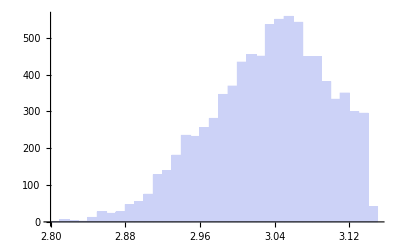

```mathematica
Histogram[angles]
```

### Find Robust Extremes of the Angle

The paper obtains "robust" extremes by taking the 1^st and 99^th percentiles of the angle data. (Why not take the peak values from the histogram?).  The paper indicates that a wide range of values can be used. Here, we can set those values as a computation option at the beginning of the file.

```mathematica
options[alpha]
```

0.01

```mathematica
Quantile[angles,options[alpha]]
```

2.87583

```mathematica
Quantile[angles,1-options[alpha]]
```

3.13836

```mathematica
findRobustExtremes[angles_,alpha_]:=
Return[{Quantile[angles,alpha],Quantile[angles,1-alpha]}]
```

```mathematica
stainAngles=findRobustExtremes[angles,options[alpha]]
```

{2.87583,3.13836}

### Convert Extreme Values Back to OD Space

This can be done by rotating the direction vector, dir1, about the normal to the plane since all the the angles were determined relative to dir1. Mathematica provides two useful functions to help with this. RotationMatrix will create a matrix to do the rotation of the desired number of radians about a given axis. RotationTransform is similar except that it returns a function that will do the rotation. Both appear to use the method of quaternions to generate the rotation matrix.

```mathematica
perp=Cross[dir1,dir2]
```

{5.81812,-90.1749,142.496}

```mathematica
RotationMatrix[stainAngles[[1]],perp]//MatrixForm
```

(-0.962556 | -0.258015 | -0.0831466
0.185598 | -0.403698 | -0.895869
0.197582 | -0.877756 | 0.436469)

```mathematica
RotationTransform[stainAngles[[1]],perp]
```

TransformationFunction[(-0.962556 | -0.258015 | -0.0831466 | 0.
0.185598 | -0.403698 | -0.895869 | 0.
0.197582 | -0.877756 | 0.436469 | 0.
0. | 0. | 0. | 1.)]

Given a vector to rotate, applying the rotation matrix produces the rotated vector.

```mathematica
RotationMatrix[stainAngles[[1]],perp].dir1//MatrixForm
```

(18.7742
25.7329
15.5178)

The following function will do the same thing and is included here so I can remember how to do it if I ever translate this into a lower level language.

```mathematica
rotateVectorAboutAxis[vector_, axis_, theta_]:=Module[
{v, a, dotpA, q, q0, q1, q2, q3,qtn,thetaDiv2},
v=Normalize[vector];
If[options[verbose]=="veryVerbose",Print["Normalized vector: ",v]];
a=Normalize[axis];
If[options[verbose]=="veryVerbose",Print["Normalized axis: ",MatrixForm[a]]];
If[options[verbose]=="veryVerbose",Print["Rotation angle (radians): ",theta]];
(* Calculate the elements of the quaternion. *)
thetaDiv2=theta/2;
q0=Cos[thetaDiv2];
q1=Sin[thetaDiv2]*a[[1]];
q2=Sin[thetaDiv2]*a[[2]];
q3=Sin[thetaDiv2]*a[[3]];
(* Build the rotation matrix. *)
q={{q0*q0+q1*q1-q2*q2-q3*q3,2*(q1*q2-q0*q3),2*(q1*q3+q0*q2)},
{2*(q2*q1+q0*q3),q0*q0-q1*q1+q2*q2-q3*q3,2*(q2*q3-q0*q1)},
{2*(q3*q1-q0*q2),2*(q3*q2+q0*q1),q0*q0-q1*q1-q2*q2+q3*q3}};
If[options[verbose]=="veryVerbose",Print["Rotation matrix: ",MatrixForm[q]]];
Flatten[q.Transpose[{vector}]]
]
```

```mathematica
sv1=rotateVectorAboutAxis[dir1,perp,stainAngles[[1]]]
```

{18.7742,25.7329,15.5178}

```mathematica
sv2=rotateVectorAboutAxis[dir1,perp,stainAngles[[2]]]
```

{10.3389,28.8271,17.8203}

```mathematica
(* A function to plot the plane formed by two vectors and plot the pixels from an image projected onto that plane along with the two color basis vectors passed in. *)
showProjectedPointsAndVectorsOnPlane[v_,w_,img_,v1_,v2_]:=Module[
{k, m,n,p,points,dkBlue,dkGreen,axes,plane,pts,vectors,mv1,mv2},
points=thresholdByBeta[convertRgbTupleArrayToOD[convertToRgbTuples[img]]];
dkBlue=RGBColor[0,0,1];
dkGreen=RGBColor[0,0.5,0];
(* A vector perpendicular to the two input vectors. *)
k=Cross[v,w];
(* Some constants used for scaling. *)
m=Round[Max[points]];
n=1.1*m;
p=-0.2;
(* The coordinate axes. *)
axes=Graphics3D[{{dkGreen,Line[{{p,0,0},{m,0,0}}],Text["x",{n,0,0}]},{dkGreen,Line[{{0,p,0},{0,m,0}}],Text["y",{0,n,0}]},{dkGreen,Line[{{0,0,p},{0,0,m}}],Text["z",{0,0,n}]}}];
(* A plot of the plane. *)
plane=Plot3D[genPlaneFunc[v,w],{x,p,n},{y,p,n},FillingStyle->Opacity[0.01],ColorFunction->plnCf];
(* A plot of the data points (pixels). *)
pts=ListPointPlot3D[projectPointsOntoPlane[points,v,w],ColorFunction->ptCf];
(* A plot of the color vectors. *)
mv1=Normalize[v1];
mv2=Normalize[v2];
vectors=
Graphics3D[
{{dkBlue,Arrow[Tube[{{0,0,0},mv1}]],Text[Style["v1", Bold],{1.2 mv1[[1]],1.2 mv1[[2]],1.2 mv1[[3]]}]},
{dkBlue,Arrow[Tube[{{0,0,0},mv2}]],
Text[Style["v2",Bold],{1.2 mv2[[1]],1.2 mv2[[2]],1.2 mv2[[3]]}]}
}];
Show[plane,pts,axes,vectors,Axes->True,AxesLabel->{"R Abs","G Abs","B Abs"}]
]
```

```mathematica
showProjectedPointsAndVectorsOnPlane[dir1,dir2,img,sv1,sv2]
```

-Graphics3D-

Hmm... It's interesting that these vectors are not where I would have placed them by eye. For example, v1 does not even seem to be within the body of the data. Changing the value of options[alpha] to 0.05 or 0.1 does seem to change the results for some images.

At this point, both the image pixels and the color basis vectors are in absorbance space. The deconvolution can occur in absorbance space. This is the same as the original method proposed by Ruifrok except that the color basis has been determined automatically.

Let's build the color basis matrix from our results so far. The method as formulated so far only produces two color weight vectors. To build a complete 3x3 matrix of weights and dyes, we can use the following function pasted from Notes on "Quantification of Histochemical Staining by Color Deconvolution" (the Ruifrok and Johnston paper.)

```mathematica
normalizeBasisRobustly[basis_]:=Module[
{m,n},
m=Table[0,{i,3},{j,3}];
n=Norm[basis[[1]]];
m[[1]]=If[n≠0,basis[[1]]/n,basis[[1]]];
n=Norm[basis[[2]]];
m[[2]]=If[n≠0,basis[[2]]/n,basis[[2]]];
n=Norm[basis[[3]]];
m[[3]]=If[n≠0,basis[[3]]/n,basis[[3]]];
m
]
```

```mathematica
(*
A function to build a color deconvolution translation matrix given at least one set of weights for a dye. Missing dyes will be created that are complementary to the dyes present until information for three dyes has been created.
*)
buildTranslationMatrix[basis_]:=Module[
{m,nr},
(* First assure that we have a basis matrix of appropriate dimensionality, i.e. 3x3, and copy over the contents of the weights. *)
m=Table[{0,0,0},{i,1,3}];
nr=First[Dimensions[basis]];
m[[1;;nr]]=basis;
If[options[verbose]=="veryVerbose",{Print["Dimensions[basis]: ",Dimensions[basis]];
Print["nr: ",nr];
Print["m: ",m//MatrixForm];}];
m=normalizeBasisRobustly[m];
If[options[verbose]=="veryVerbose",Print["normalized m: ",m//MatrixForm]];
(* If second dye is unspecified, copy the first into it. *)
If[Norm[m[[2]]==0],m[[2]]=m[[1]]];
(* If third dye is unspecified fill with the complement of the others. *)
If[Norm[m[[3]]]==0,
{If[options[verbose]=="veryVerbose",Print["Filling third row"]];
If[m[[1,1]]*m[[1,1]]+m[[2,1]]*m[[2,1]]>1,{
If[options[verbose]=="veryVerbose",Print["Color 3 has negative R component"]];
m[[3,1]]=0;},
m[[3,1]]=Sqrt[1.0-m[[1,1]]*m[[1,1]]-m[[2,1]]*m[[2,1]]]];
If[m[[1,2]]*m[[1,2]]+m[[2,2]]*m[[2,2]]>1,{
If[options[verbose]=="veryVerbose",Print["Color 3 has negative G component"]];
m[[3,2]]=0;},
m[[3,2]]=Sqrt[1.0-m[[1,2]]*m[[1,2]]-m[[2,2]]*m[[2,2]]]];
If[m[[1,3]]*m[[1,3]]+m[[2,3]]*m[[2,3]]>1,{
If[options[verbose]=="veryVerbose",Print["Color 3 has negative G component"]];
m[[3,3]]=0;},
m[[3,3]]=Sqrt[1.0-m[[1,3]]*m[[1,3]]-m[[2,3]]*m[[2,3]]]];
(* Set any zero elements to a small positive number. *)
m=m/. 0->0.001;
If[options[verbose]=="veryVerbose",Print["m without zeros: ",m//MatrixForm]];
(* Normalize third dye color *)
m[[3]]=m[[3]]/Norm[m[[3]]];
}];
m
]
```

```mathematica
basis=buildTranslationMatrix[{Normalize[sv1],Normalize[sv2]}];
basis//MatrixForm
```

(0.529859 | 0.726254 | 0.437955
0.291791 | 0.81358 | 0.502937
0.730172 | 0.000916946 | 0.683263)

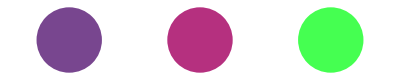

```mathematica
Graphics[{RGBColor[1-basis[[1]]],Disk[{0,0},0.25],RGBColor[1-basis[[2]]],Disk[{1,0},0.25],RGBColor[1-basis[[3]]],Disk[{2,0},0.25]}]
```

These appear to be reasonable colors for the dyes.

```mathematica
nb=Inverse[basis];
nb//MatrixForm
```

(3.55687 | -3.17515 | 0.0573056
1.07495 | 0.270566 | -0.888177
-3.8025 | 3.39278 | 1.40352)

Do the deconvolution. We have to go back and get the entire array of image data and convert it to absorbance first.

```mathematica
completeOdPts=convertRgbTupleArrayToOD[convertToRgbTuples[img]];
```

```mathematica
deconvAbsPts=completeOdPts.nb;
```

```mathematica
convertOdToRgb[od_]:=N[Power[10,-od]];
convertOdTupleToRgb[tuple_]:=convertOdToRgb/@ tuple;
convertOdTupleArrayToRgb[tuples_]:=convertOdTupleToRgb/@ tuples;
```

```mathematica
deconvTransPts=convertOdTupleArrayToRgb[deconvAbsPts];
```

Put the data back in the shape of the original image.

```mathematica
arr = Partition[deconvTransPts, Part[Dimensions[ImageData[img]],2]];
```

```mathematica
Dimensions[arr]
```

{100,100,3}

```mathematica
outputImage=Image[arr,ColorSpace->"RGB"]
```

-Graphics-

```mathematica
csi=ColorSeparate[outputImage]
```

{-Graphics-,-Graphics-,-Graphics-}

This appears to be a pretty good deconvolution with very little color "left over" in the third channel.

The images of the deconvolved dyes can be colorized with the following function pasted from Notes on "Quantification of Histochemical Staining by Color Deconvolution".

```mathematica
(*
Given a grayscale image and a set of RGB weights for the hue,produce a version of the image with the pixels colored with the intensity of the output hue being related to the darkness of the input gray pixels.
Input: 
img -- a grayscale image.
weights -- a list of the relative weights of the RGB channels for the desired hue.
Output: a new image colored with the desired hue.
*)
colorizeGrayImage[img_,weights_]:=Module[
{grayData,lut,rgbTuples,arr,newImg},
If[options[verbose]=="veryVerbose",Print["weights: ",weights]];
lut=Reverse[Table[{(255-(i*weights[[1]]))/255,(255-(i*weights[[2]]))/255,(255-(i*weights[[3]]))/255},{i,0,255}]];
If[options[verbose]=="veryVerbose",
{Print["Dimensions[lut]: ",Dimensions[lut]];Print["lut: ", Take[lut,5],", ..."]}];
grayData=Flatten[ImageData[img,"Byte"]];
If[options[verbose]=="veryVerbose",
{Print["Dimensions[grayData]: ",Dimensions[grayData]];Print["grayData: ",Take[grayData,5], ", ..."]}];
(* Create a new list of RGB values by mapping the grayscale data through the lookup table. *)
rgbTuples=lut[[#+1]]&/@grayData;
If[options[verbose]=="veryVerbose",{Print["Dimensions[rgbTuples]: ",Dimensions[rgbTuples]];
Print["rgbTuples: ", Take[rgbTuples,5],", ..."]}];
arr = Partition[rgbTuples, Part[Dimensions[ImageData[img]],2]];
If[options[verbose]=="veryVerbose",{Print["Max[arr]: ",Max[arr],", Min[arr]: ",Min[arr]];
Print["Dimensions[arr]: ", Dimensions[arr]]}];
newImg=Image[arr,ColorSpace->"RGB"];
If[options[verbose]=="veryVerbose",{Print["ImageQ[newImg]: ", ImageQ[newImg]];
Print["ImageType[newImg]: ",ImageType[newImg]];
Print["ImageChannels[newImg]: ",ImageChannels[newImg]]}];
newImg
]
```

```mathematica
(*
Create three colored images from an input list of grayscale images and a matrix of RGB weights. Each row of the weight matrix corresponds to the hue to be applied to the corresponding image.
*)
colorizeGrayImages[imgList_,weightMatrix_]:=
{colorizeGrayImage[imgList[[1]],weightMatrix[[1]]],
colorizeGrayImage[imgList[[2]],weightMatrix[[2]]],
colorizeGrayImage[imgList[[3]],weightMatrix[[3]]]}
```

```mathematica
colorizeGrayImages[csi,basis]
```

{-Graphics-,-Graphics-,-Graphics-}

### Packaging the Deconvolution in a Single Function

The steps outlined in the notes above can be packaged into a single function.

```mathematica
deconvolveByMacenko[img_]:=Module[
{odPixels,threshOdPixels,u,s,v,scaledDirections,dir1,dir2,prjPts,angles,stainAngles,perp,sv1,sv2,basis,deconvAbsPts,deconvTransPts,arr},
odPixels=convertRgbTupleArrayToOD[convertToRgbTuples[img]];
If[options[verbose]=="veryVerbose",Print["Dimensions[odPixels]: ",Dimensions[odPixels]]];
threshOdPixels=thresholdByBeta[odPixels];
If[options[verbose]=="veryVerbose",Print["Dimensions[threshOdPixels]: ",Dimensions[threshOdPixels]]];
{u,s,v}=SingularValueDecomposition[threshOdPixels,2];
If[options[verbose]=="veryVerbose",Print["s: ",s//MatrixForm,", v: ",v//MatrixForm]];
scaledDirections=v.s;
If[options[verbose]=="veryVerbose",Print["scaledDirections: ",scaledDirections//MatrixForm]];
dir1=scaledDirections[[All,1]];
dir2=scaledDirections[[All,2]];
prjPts=projectAndNormalizePointsOntoPlane[threshOdPixels,dir1,dir2];
If[options[verbose]=="veryVerbose",Print["Dimensions[prjPts]: ",Dimensions[prjPts]]];
angles=calcProjectedAngles[dir1,prjPts];
stainAngles=findRobustExtremes[angles,options[alpha]];
If[options[verbose]=="veryVerbose",Print["Extreme angles: ", stainAngles]];
perp=Cross[dir1,dir2];
sv1=rotateVectorAboutAxis[dir1,perp,stainAngles[[1]]];
sv2=rotateVectorAboutAxis[dir1,perp,stainAngles[[2]]];
If[options[verbose]=="veryVerbose",{Print["sv1: ",sv1];Print["sv2: ",sv2]}];
basis=buildTranslationMatrix[{Normalize[sv1],Normalize[sv2]}];
If[options[verbose]=="veryVerbose",Print["basis: ", basis//MatrixForm]];
deconvAbsPts=odPixels.Inverse[basis];
deconvTransPts=convertOdTupleArrayToRgb[deconvAbsPts];
arr=Partition[deconvTransPts,Part[Dimensions[ImageData[img]],2]];
{Image[arr,ColorSpace->"RGB"],basis}
]
```

```mathematica
{outImg, outBasis}=deconvolveByMacenko[img];
colorizeGrayImages[ColorSeparate[outImg],outBasis]
```

{-Graphics-,-Graphics-,-Graphics-}

Now let's try on a different, larger image. (Note: Again, you may have to change the following path to the image file to match the setup on your machine.)

```mathematica
bigImgPath = "C:\\projects\\color-deconvolution\\Images\\S09-16877_ER_200906060903-3.jpg";
bigImg = Import[bigImgPath]
```

-Graphics-

```mathematica
{outImg,outBasis}=deconvolveByMacenko[bigImg];
(*options[verbose]="veryVerbose";*)
colorizeGrayImages[ColorSeparate[outImg],outBasis]
```

{-Graphics-,-Graphics-,-Graphics-}

That seems pretty good. However, the method can be fooled.